# Total Aberrations

```mathematica
Off[General::spell1]
Off[General::spell]
Off[∞::indet]
Off[Power::infy]
Off[Simplify::infd]

TotalAberrations[rad_,thick_,ind_,costasf_,stoprad_,nstop_,dis_,dobject_,hobject_,angle_,waves_,option1_]:=
Module[{},
(* number of surfaces and wave lengths *)
n=Length[rad];
m=Length[waves];

(* Distances among the surfaces *)
thicke=Reverse[Take[thick,{1,nstop-1}]];
thicke1=Join[thicke,{0}];
rade=-Reverse[Take[rad,{1,nstop}]]//Flatten;

(* Evaluation of the aperture stop images supplied by the surfaces preceeding the stop:
the last one is the entrance pupil. *)
Do[
inde[h]=Reverse[Take[ind[[h]],{1,nstop}]];
inde1[h]=Prepend[inde[h],1],
{h,1,m}];


Do[
ze[h,1]=If[nstop===0,dis,-dis],
{h,1,3}];

Do[
Do[
Qe[h,i]=(inde1[h][[i]])/ze[h,i]-(inde1[h][[i]])/rade[[i]]-(inde1[h][[i+1]])/w1[h,i]+(inde1[h][[i+1]])/rade[[i]];
ze1[h,i]=Which[ze[h,i]===0,ze[h,i],ze[h,i]===-Infinity&&Abs[rad[[i]]]===Infinity,-Infinity,ze[h,i]=!=-Infinity&&Simplify[Numerator[Together[(inde1[h][[i]])/ze[h,i]-(inde1[h][[i]])/rad[[i]]+(inde1[h][[i+1]])/rad[[i]]]]]===0,-Infinity,ze[h,i]=!=-Infinity||ze[h,i]===-Infinity,Solve[Qe[h,i]==0,w1[h,i]][[1,1,2]]]; ze[h,i+1]=ze1[h,i]-thicke1[[i]],
{i,1,nstop}],
{h,1,m}];
Do[
de[h]=Which[nstop===0,dis,nstop=!=0,-ze1[h,nstop]],
{h,1,3}];

If[option1==1,Print["Distance of entrance pupil from the first surface for λ = ",waves[[1]]]];
If[option1==1,Print["w_e = ", de[1](*//Simplify*)]];

Do[
ye[h,1]=stoprad;
Do[
ye1[h,i]=If[ze[h,i]=!=0,(inde1[h][[i]] ze1[h,i])/(inde1[h][[i+1]] ze[h,i])ye[h,i],ye[h,i]];
ye[h,i+1]=ye1[h,i],
{i,1,nstop}];
diame[h]=Which[nstop===0,stoprad,nstop=!=0,ye1[h,nstop]],
{h,1,m}];

If[option1==1,Print["Radius of entrance pupil for λ = ",waves[[1]]]];
If[option1==1,Print["r_en = ",diame[1]]];

(* Evaluation of exit pupil *)
thick2=Join[thick,{0}];
Do[
zee[h,1]=de[h];
Do[zee1[h,i]=Which[zee[h,i]===0,0,zee[h,i]===-Infinity&&Abs[rad[[i]]]===Infinity,-Infinity,zee[h,i]=!=-Infinity&&ind[[h,i]]/zee[h,i]-ind[[h,i]]/rad[[i]]+ind[[h,i+1]]/rad[[i]]===0,-Infinity,zee[h,i]=!=-Infinity||zee[h,i]===-Infinity,Solve[Numerator[Together[ind[[h,i]]/zee[h,i]-ind[[h,i]]/rad[[i]]-ind[[h,i+1]]/fe1[h,i]+ind[[h,i+1]]/rad[[i]]]]==0,fe1[h,i]][[1]][[1,2]]];zee[h,i+1]=zee1[h,i]-thick2[[i]],
{i,1,n}],{h,1,m}];

If[option1==1,Print["Distance of the exit pupil from the last surface for λ = ",waves[[1]]]];
If[option1==1,Print["w_(e, n) = ",zee1[1,n](*//Simplify*)]];

Do[
yee[h,1]=diame[h];
Do[
yee1[h,i]=Which[zee[h,i]=!=0,(ind[[h,i]] zee1[h,i])/(ind[[h,i+1]] zee[h,i])yee[h,i],zee[h,i]===0,yee[h,i]];
yee[h,i+1]=yee1[h,i],{i,1,n}],
{h,1,m}];

If[option1==1,Print["Radius of exit pupil for λ = ",waves[[1]]]];
If[option1==1,Print["r_ex = ",Abs[ yee1[1,n]]]];

(* Pupil Magnification  *)

Do[
Do[
Mae[h,i]=yee1[h,i]/yee[h,1],
{i,1,n}],
{h,1,m}];

(*Principal planes and focal length*)
Do[
Do[P[h,i]=(ind[[h,i+1]]-ind[[h,i]])/rad[[i]];
R0[h,i]={{1,0},{(-P[h,i])/ind[[h,i+1]],ind[[h,i]]/ind[[h,i+1]]}},
{i,1,n}],
{h,1,m}];


If[n==1,Goto[1],Goto[2]];

Label[1];
Do[Mt[h]=R0[h,1],{h,1,m}];

Goto[3];

Label[2];
(*Total matrix of the i-th surface*)

Do[D0[i]={{1,thick[[i]]},{0,1}},{i,1,n-1}];
Do[
Do[
B0[h,i]=If[i<n,D0[i].R0[h,i],R0[h,n]],{i,1,n}],{h,1,m}];

(*Matrices of the sub-systems*)
Do[
Do[
b[h,1]=B0[h,1];
b[h,i]=B0[h,i].b[h,i-1],
{i,2,n}],{h,1,m}];

(*Total matrix of the system*)
Do[Mt[h]=b[h,n],{h,1,m}];
Label[3];


(*Distances of the principal planes from the first and last surface, respectively*)


Do[
zp[h]=If[Mt[h][[2,1]]===0,0,1/(Mt[h][[2,1]])(Mt[h][[1,2]]Mt[h][[2,1]]+Mt[h][[2,2]]-Mt[h][[1,1]]Mt[h][[2,2]])];
z1p[h]=If[Mt[h][[2,1]]===0,0,(1-Mt[h][[1,1]])/(Mt[h][[2,1]])],{h,1,m}];
(***********************************)
If[option1===1,Print["Distance of the first principal plane from the first surface = ",zp[1]]];
If[option1===1,Print["Distance of the second principal plane from the last surface = ",z1p[1]]];

(* Distances of the images *)


Do[zog[h,1]=dobject,{h,1,m}];

Do[
Do[zog1[h,i]=Which[rad[[i]]=!=Infinity&&zog[h,i]=!=-Infinity&&Simplify[(ind[[h,i+1]] rad[[i]] zog[h,i])/(ind[[h,i]]rad[[i]]-ind[[h,i]]zog[h,i]+ind[[h,i+1]] zog[h,i])]=!=ComplexInfinity,Simplify[(ind[[h,i+1]] rad[[i]] zog[h,i])/(ind[[h,i]]rad[[i]]-ind[[h,i]]zog[h,i]+ind[[h,i+1]] zog[h,i])],

rad[[i]]=!=Infinity&&zog[h,i]=!=-Infinity&&Simplify[(ind[[h,i+1]] rad[[i]] zog[h,i])/(ind[[h,i]]rad[[i]]-ind[[h,i]]zog[h,i]+ind[[h,i+1]] zog[h,i])]===ComplexInfinity,-Infinity,rad[[i]]===Infinity&&zog[h,i]=!=-Infinity,(ind[[h,i+1]]zog[h,i])/ind[[h,i]],rad[[i]]=!=Infinity&&zog[h,i]===-Infinity,(ind[[h,i+1]] rad[[i]])/(-ind[[h,i]]+ind[[h,i+1]]),rad[[i]]===Infinity&&zog[h,i]===-Infinity,-Infinity];zog[h,i+1]=zog1[h,i]-thick2[[i]],{i,1,n}],{h,1,m}];
If[option1==1,Print["Gaussian distances of the images from the surfaces for λ = ",waves[[1]]]];
If[option1==1,Print[Table[zog1[1,i],{i,1,n}]]];

(*Focal length *)
Do[zoginf[h,1]=-Infinity,{h,1,m}];
Do[
Do[zog1inf[h,i]=Which[rad[[i]]=!=Infinity&&zoginf[h,i]=!=-Infinity&&Simplify[(ind[[h,i+1]] rad[[i]] zoginf[h,i])/(ind[[h,i]]rad[[i]]-ind[[h,i]]zoginf[h,i]+ind[[h,i+1]] zoginf[h,i])]=!=ComplexInfinity,Simplify[(ind[[h,i+1]] rad[[i]] zoginf[h,i])/(ind[[h,i]]rad[[i]]-ind[[h,i]]zoginf[h,i]+ind[[h,i+1]] zoginf[h,i])],

rad[[i]]=!=Infinity&&zoginf[h,i]=!=-Infinity&&Simplify[(ind[[h,i+1]] rad[[i]] zoginf[h,i])/(ind[[h,i]]rad[[i]]-ind[[h,i]]zoginf[h,i]+ind[[h,i+1]] zoginf[h,i])]===ComplexInfinity,-Infinity,rad[[i]]===Infinity&&zoginf[h,i]=!=-Infinity,(ind[[h,i+1]]zoginf[h,i])/ind[[h,i]],rad[[i]]=!=Infinity&&zoginf[h,i]===-Infinity,(ind[[h,i+1]] rad[[i]])/(-ind[[h,i]]+ind[[h,i+1]]),rad[[i]]===Infinity&&zoginf[h,i]===-Infinity,-Infinity];zoginf[h,i+1]=zog1inf[h,i]-thick2[[i]],{i,1,n}];,{h,1,m}];
Do[foc[h]=zog1inf[h,n]-z1p[h],{h,1,m}];
If[option1===1, Print["Focal length = ",foc[1]]];

dinf=Cases[rad,Infinity];
If[Length[dinf]>0,Goto[lab]];

(*Height of images *)
Do[hobj1[h,1]=If[dobject===-Infinity,(ind[[h,1]] zog1[h,1])/ind[[h,2]] π/180 angle,(ind[[h,1]] zog1[h,1])/(ind[[h,2]]zog[h,1])hobject],{h,1,m}];
Do[Do[hobj[h,i]=hobj1[h,i-1];hobj1[h,i]=(ind[[h,i]] zog1[h,i])/(ind[[h,i+1]]zog[h,i])hobj[h,i] ,{i,2,n}],{h,1,m}];


If[option1==1,Print["Image height = ",hobj1[1,n]]];

Label[lab];
(*Aberrations *)


Do[
Do[
C1[h,i]=If[Length[costasf[[i]]]==2,-costasf[[i,1]](ind[[h,i+1]]-ind[[h,i]])+(ind[[h,i+1]]-ind[[h,i]])/(8 rad[[i]]^3)-ind[[h,i]]^2/8(1/(ind[[h,i+1]]zog1[h,i])-1/(ind[[h,i]]zog[h,i]))(1/zog[h,i]-1/rad[[i]])^2,-costasf[[i]](ind[[h,i+1]]-ind[[h,i]])/(8 rad[[i]]^3)-ind[[h,i]]^2/8(1/(ind[[h,i+1]]zog1[h,i])-1/(ind[[h,i]]zog[h,i]))(1/zog[h,i]-1/rad[[i]])^2],
{i,1,n}],
{h,1,m}];

(*Coefficients of coma for stop on the surface*)
Do[
Do[
C2[h,i]=ind[[h,i]]^2/2(1/(ind[[h,i+1]]zog1[h,i])-1/(ind[[h,i]]zog[h,i]))(1/zog[h,i]-1/rad[[i]]),
{i,1,n}],
{h,1,m}];


(* Coefficients of fields curvature and astigmatism for stop on the surface *)

Do[
Do[
C3[h,i]=ind[[h,i]]/4(ind[[h,i+1]]^2-ind[[h,i]]^2)/ind[[h,i+1]]^2(1/zog[h,i]-1/rad[[i]]);
C4[h,i]=(-ind[[h,i]]^2)/2(1/(ind[[h,i+1]]zog1[h,i])-1/(ind[[h,i]]zog[h,i]))+C3[h,i],
{i,1,n}],
{h,1,m}];

(*Coefficients of distorsion for stop on the surface *)

Do[
Do[
C5[h,i]=-ind[[h,i]]/2(ind[[h,i+1]]^2-ind[[h,i]]^2)/ind[[h,i+1]]^2,
{i,1,n}],
{h,1,m}];


(* Aberration Coefficients depending on the stop position *)

Do[
Do[
c1[h,i]=If[zog[h,i]===-Infinity,1,zog[h,i]/(zog[h,i]-zee[h,i])];
d1[h,i]=If[zog[h,i]===-Infinity,0,zee[h,i]/(zog[h,i]-zee[h,i])];
k1[h,i]=If[zog[h,i]===-Infinity,zee[h,i],zog[h,i] d1[h,i]];
Cd1[h,i]=c1[h,i]^4 C1[h,i];
Cd2[h,i]=c1[h,i]^2(C2[h,i]-4k1[h,i]C1[h,i]);
Cd3[h,i]=(C3[h,i]-k1[h,i]C2[h,i]+2 k1[h,i]^2 C1[h,i]);
Cd4[h,i]=(C4[h,i]-3k1[h,i]C2[h,i]+6 k1[h,i]^2 C1[h,i]);
Cd5[h,i]=1/c1[h,i]^2(C5[h,i]-2k1[h,i]C4[h,i]+3 k1[h,i]^2 C2[h,i]-4 k1[h,i]^3 C1[h,i]),
{i,1,n}],
{h,1,m}];


(*Compound system*)
(* Field angle *)
Do[
theta[h]=If[dobject===-Infinity,π/180 angle,hobject/(dobject-zee[h,1])],
{h,1,m}];

(*Total spherical aberration *)

Do[
Do[
Absfer[h,i]=If[i==1,4(zog1[h,n]-zee1[h,n])/ind[[h,n+1]] 1/Mae[h,n] Cd1[h,1] yee[h,1]^3,4(zog1[h,n]-zee1[h,n])/ind[[h,n+1]] 1/Mae[h,n] Cd1[h,i] Mae[h,i-1]^4 yee[h,1]^3],
{i,1,n}],{h,1,m}];

Do[
Seidsphe[h]=(Cd1[h,1]+Sum[Cd1[h,i] Mae[h,i-1]^4,{i,2,n}]),
{h,1,m}];
If[option1==0,Print["Spherical coefficient"]];
If[option1==0,Print[Simplify[Seidsphe[1]]]];
Do[Absftot[h]=Sum[Absfer[h,i],{i,1,n}],{h,1,m}];
If[option1==1,Do[Print["Total spherical aberration = ",Simplify[Absftot[h]],"    ( λ = ",waves[[h]]," )"], {h,1,m}]];

(*Total sagittal coma *)
Do[Comapar[h,1]=(zog1[h,n]-zee1[h,n])/ind[[h,n+1]] 1/Mae[h,n] Cd2[h,1] theta[1](yee[h,1])^2,{h,1,m}];

Do[Comapar[h,i]=(zog1[h,n]-zee1[h,n])/ind[[h,n+1]] 1/Mae[h,n] ind[[h,1]]/ind[[h,i]](Mae[h,i-1])^2 Cd2[h,i] theta[h](yee[h,1])^2,{i,2,n},{h,1,m}];
Do[Seidcoma[h]=Cd2[h,1]+Sum[ind[[h,1]]/ind[[h,i]](Mae[h,i-1])^2 Cd2[h,i],{i,2,n}],{h,1,m}];


If[option1==0,Print["Coma coefficient "]];
If[option1==0,Print[Simplify[Seidcoma[1]]]];
Do[ Comatot[h] =Sum[Comapar[h,i],{i,1,n}],{h,1,m}];

If[option1==1,Do[Print["Total coma  = ",Simplify[Comatot[h]], "   ( λ = ",waves[[h]], " )"], {h,1,m}]];




(* Astigmatism *)
Do[Astpar[h,1]=(zog1[h,n]-zee1[h,n])/ind[[h,n+1]] 1/Mae[h,n](Cd4[h,1]-Cd3[h,1]) (theta[h])^2 yee[h,1],{h,1,m}];

Do[
Astpar[h,i]=(zog1[h,n]-zee1[h,n])/ind[[h,n+1]] 1/Mae[h,n](ind[[h,1]]/ind[[h,i]])^2(Cd4[h,i]-Cd3[h,i]) (theta[h])^2 yee[h,1],
{i,2,n},{h,1,m}];

Do[Seidast[h]=Sum[(ind[[h,1]]/ind[[h,i]])^2(Cd4[h,i]-Cd3[h,i]),{i,1,n}],{h,1,m}];

If[option1==0,Print["Astigmatism coefficient = ",Simplify[Seidast[1]]]];


Do[Asttot[h] =Sum[Astpar[h,i],{i,1,n}],{h,1,m}];


If[option1==1,Do[Print["Total astigmatism  = ",Simplify[Asttot[h]], "     ( λ = ",waves[[h]]," )"],{h,1,m}]];

Do[
Sp[h,i]=ind[[h,n+1]]/rad[[i]](1/ind[[h,i+1]]-1/ind[[h,i]]),
{i,1,n},{h,1,m}];
Do[Seidcurv[h]= Sum[ind[[h,1]]^2/Mae[h,n] Sp[h,i]/2, {i,1,n}],{h,1,m}];
Do[Curvpar[h,i]=(zog1[h,n]-zee1[h,n])/ind[[h,n+1]]^2 ind[[h,1]]^2/Mae[h,n] Sp[h,i]/2 theta[h]^2 yee[h,1],{i,1,n},{h,1,m}];


Do[Curvtot[h]=Sum[Curvpar[h,i],{i,1,n}],
{h,1,m}];
If[option1==1,Print["Total curvature = ", Curvtot[1]]];

Do[
Do[Sp[h,i]=ind[[h,n+1]]/rad[[i]](1/ind[[h,i+1]]-1/ind[[h,i]]),{i,1,n}],
{h,1,m}];
Do[Petzval[h]=1/Sum[Sp[h,i],{i,1,n}],{h,1,m}];
If[option1==1,Print["Petzval radius = ", Petzval[1]]];


(* Distorsion *)
Do[
Distpar[h,1]=(zog1[h,n]-zee1[h,n])/ind[[h,n+1]] 1/Mae[h,n] Cd5[h,1] theta[h]^3,{h,1,m}];
Do[
Distpar[h,i]=(zog1[h,n]-zee1[h,n])/ind[[h,n+1]] 1/Mae[h,n](ind[[h,1]]/ind[[h,i]])^3 Cd5[h,i] 1/Mae[h,i-1]^2 theta[h]^3 ,
{i,2,n},{h,1,m}];
Do[Seiddist[h] =1/Mae[h,n] Cd5[h,1]+Sum[1/Mae[h,n](ind[[h,1]]/ind[[h,i]])^3 Cd5[h,i] 1/Mae[h,i-1]^2,{i,2,n}],
{h,1,m}];
Do[Disttot[h]=(zog1[h,n]-zee1[h,n])/ind[[h,n+1]] Seiddist[h] theta[h]^3,{h,1,m}];
If[option1==1,Print["Total distorsion = ",Simplify[Disttot[1]]]];


]
```

# Higher-Order Aberrations

```mathematica
(*Off[FindRoot::lstol]*)

HOrdAberrations[rad_,thick_,ind_,costasf_,stoprad_,nstop_,dis_,dobject_,hobject_,angle_,waves_,opt_]:=
Module[{},
TotalAberrations[rad,thick,ind,costasf,stoprad,nstop,dis,dobject,hobject,angle,waves,2];



(* Evaluation of aberrations *)

(*Equations of the surfaces*)

spess=Join[{0},Table[Sum[thick[[h]],{h,1,j}],{j,1,n-1}]];
Do[
Which[Length[costasf[[j]]]==2,Fu[j]=spess[[j]]+1/(2 rad[[j]])(x^2+y^2) +costasf[[j]][[1]](x^2+y^2)^2,
rad[[j]]===Infinity,Fu[j]=spess[[j]],
rad[[j]]>0,Fu[j]=If[costasf[[j]]==-1,spess[[j]]+(x^2+y^2)/(2rad[[j]]),spess[[j]]+(rad[[j]]-√(rad[[j]]^2-(x^2+y^2)(1+costasf[[j]])))/(1+costasf[[j]])],
rad[[j]]<0,
Fu[j]=If[costasf[[j]]==-1,spess[[j]]+(x^2+y^2)/(2rad[[j]]),spess[[j]]+(rad[[j]]+√(rad[[j]]^2-(x^2+y^2)(1+costasf[[j]])))/(1+costasf[[j]])]],{j,1,n}];


(* In the sequel, the index p denotes an object point on the Oy axis, whereas k,j fix the coordinates of the points in the entrance pupil. Finally, i denotes the i-th surface of the optical system. *)

nr=3;
div=2;

(* Points in the entrance pupil*)
Do[Do[r[h,k]=k diame[h]/10;ϕ[j]=j π/4,{k,0,nr},{j,-1,1}],{h,1,m}];
Do[Do[pm[h,p,k,j,0]={r[h,k]Cos[ϕ[j]],r[h,k]Sin[ϕ[j]]},{p,0,div},{k,0,nr},{j,-1,1}],{h,1,m}]//N;

(* The unit vectors of the entering rays *)

Do[
verm[h,p,k,j,0]=If[dobject===-Infinity,N[{0,Sin[p/6 angle π/180],Cos[p/6 angle π/180]}], y[p]=p hobject/div;N[{pm[h,k,j,0][[1]]/(√((pm[h,k,j,0][[1]])^2+(pm[h,k,j,0][[2]]-y[p])^2+(de[h]-dobject)^2)),(pm[h,k,j,0][[2]]-y[p])/(√((pm[h,k,j,0][[1]])^2+(pm[h,k,j,0][[2]]-y[p])^2+(de[h]-dobject)^2)),(de[h]-dobject)/(√((pm[h,k,j,0][[1]])^2+(pm[h,k,j,0][[2]]-y[p])^2+(de[h]-dobject)^2))}]],{h,1,m},{p,0,div},{k,0,nr},{j,-1,1}];


(* Equations of the entering rays *)

Do[eqm[h,p,k,j,0]={pm[h,p,k,j,0][[1]],pm[h,p,k,j,0][[2]],de[h]}+verm[h,p,k,j,0]par,{h,1,m},{p,0,div},{k,0,nr},{j,-1,1}];


(* Ray tracing of the rays: global coordinates*)

Do[equazm[h,p,k,j,i]=eqm[h,p,k,j,i-1][[3]]==spess[[i]];
solm0[h,p,k,j,i]=Solve[equazm[h,p,k,j,i],par]//Flatten;
solm[h,p,k,j,i]=FindRoot[eqm[h,p,k,j,i-1][[3]]==(Fu[i]/.{x->eqm[h,p,k,j,i-1][[1]],y->eqm[h,p,k,j,i-1][[2]]}),{par,solm0[h,p,k,j,i][[1,2]]},AccuracyGoal->10^(-5)];
pm[h,p,k,j,i]={eqm[h,p,k,j,i-1][[1]],eqm[h,p,k,j,i-1][[2]],eqm[h,p,k,j,i-1][[3]]}/.solm[h,p,k,j,i];
mum[h,p,k,j,i]=(1/Sqrt[1+(D[Fu[i],x])^2+(D[Fu[i],y])^2]//.{x->pm[h,p,k,j,i][[1]],y->pm[h,p,k,j,i][[2]]});
norm[h,p,k,j,i]=mum[h,p,k,j,i]{-D[Fu[i],x],-D[Fu[i],y],1}//.{x->pm[h,p,k,j,i][[1]],y->pm[h,p,k,j,i][[2]]};
csm[h,p,k,j,i]=norm[h,p,k,j,i].verm[h,p,k,j,i-1];
snm[h,p,k,j,i]=Sqrt[1-csm[h,p,k,j,i]^2];
λm[h,p,k,j,i]=ind[[h,i+1]] √(1-((ind[[h,i]]snm[h,p,k,j,i])/ind[[h,i+1]])^2)-ind[[h,i]]csm[h,p,k,j,i];
verm[h,p,k,j,i]=1/ind[[h,i+1]](ind[[h,i]]verm[h,p,k,j,i-1]+λm[h,p,k,j,i] norm[h,p,k,j,i]);
eqm[h,p,k,j,i]=pm[h,p,k,j,i]+verm[h,p,k,j,i]*par,{h,1,m},{p,0,div},{k,0,nr},{j,-1,1},{i,1,n}];



(* Global coordinates of the intersection points of the rays with the Gaussian image plane *)
Do[
Do[somG[h,p,k,j]=Solve[eqm[h,p,k,j,n][[3]]==spess[[n]]+zog1[1,n],par][[1]];
xmG[h,p,k,j]=eqm[h,p,k,j,n][[1]]/.somG[h,p,k,j];
ymG[h,p,k,j]=eqm[h,p,k,j,n][[2]]/.somG[h,p,k,j] ,{p,0,div},{k,0,nr},{j,-1,1}],{h,1,m}];

(* The aberrations will be expressed in terms of the field angle θ1 and the coordinates in the entrance pupil. *)
Do[θ1[p]=If[dobject===-Infinity,p/6 angle π/180,ArcTan[y[p]/(dobject-de[1])]],{p,0,div}];
Do[ϕ[j]=j π/4,{j,-1,1}];
(*Evaluation of third order aberrations *)

Do[
ϵ3x[p,k,j]=(zog1[1,n]-zee1[1,n])/ind[[1,n+1]] 1/Mae[1,n](4Seidsphe[1](r[1,k])^3 Cos[ϕ[j]]+Seidcoma[1](r[1,k])^2 θ1[p]Sin[2ϕ[j]]+Sum[(ind[[1,1]]/ind[[1,i]])^2 Cd3[1,i],{i,1,n}]r[1,k](θ1[p])^2 Cos[ϕ[j]]);
ϵ3y[p,k,j]=(zog1[1,n]-zee1[1,n])/ind[[1,n+1]] 1/Mae[1,n](4Seidsphe[1](r[1,k])^3 Sin[ϕ[j]]+Seidcoma[1](r[1,k])^2 θ1[p](2-Cos[2ϕ[j]])+Sum[(ind[[1,1]]/ind[[1,i]])^2 Cd4[1,i],{i,1,n}]r[1,k](θ1[p])^2 Sin[ϕ[j]]+Sum[(ind[[1,1]]/ind[[1,i]])^3 Cd5[1,i],{i,1,n}](θ1[p])^3),{p,0,div},{k,0,nr},{j,-1,1}];
(* Residual aberrations *)

Do[aberr[p,k,j]=xmG[1,p,k,j]-ϵ3x[p,k,j],{p,0,div},{k,0,nr},{j,-1,1}];

(*Higher-order spherical aberration *)
syssf=Table[((a1 x^5+b x^7+c x^9)/.x->r[1,k])==xmG[1,0,k,0]-ϵ3x[0,k,0],{k,1,nr}];
sosf=NSolve[syssf,{a1,b,c}]//Flatten;
sfer5=(sosf[[1,2]]x^5)/.x->diame[1];
If[opt==2,Goto[lab],
Print["Third-order spherical aberration = ",Absftot[1]//N];
Print["Fifth-order spherical aberration = ",sfer5];
Print["Third-order coma = ",Comatot[1]//N]];

Label[lab];
(*Fifth-order Coma *)
fact=r[1,nr]/(θ1[div]*π/180);
equaz1=(2a2 x^4 θ +2a5 x^2 θ^3);
sys1=Simplify[Table[(equaz1/.{x->r[1,nr],θ->fact θ1[p]})==xmG[1,p,nr,1]-ϵ3x[p,nr,1]-(xmG[1,p,nr,-1]-ϵ3x[p,nr,-1]),{p,1,div}]];

sco=Solve[sys1,{a2,a5}]//Flatten;
coma5=sco[[1,2]] fact x^4 θ/.{x->diame[1],θ->angle π/180};
If[opt==2,Goto[abc],
Print["Fifth-order coma = ",coma5]];
(*
(*Other fifth-order coefficients *)
equaz2=(√2 a1 x^5+√2 A x^3 θ^2+√2 a6 x θ^4+b x^7)/.sosf;
equaz21=(equaz2/.{x->r[1,3],θ->fact θ1[2]})==xmG[1,2,3,1]-ϵ3x[2,3,1]+(xmG[1,2,3,-1]-ϵ3x[2,3,-1]);
equaz22=(equaz2/.{x->r[1,1],θ->fact θ1[4]})==xmG[1,4,1,1]-ϵ3x[4,1,1]+(xmG[1,4,1,-1]-ϵ3x[4,1,-1]);
sco2=NSolve[{equaz21,equaz22},{A,a6}]//Flatten;
*)
Label[abc];
]
```

# MarginaRayTracing

```mathematica
(*Off[FindRoot::lstol]*)

MarginalRayTracing[rad_,thick_,ind_,costasf_,stoprad_,nstop_,dis_,dobject_,hobject_,angle_,waves_,opt_]:=
Module[{},
(* number of surfaces and wave lengths *)
TotalAberrations[rad,thick,ind,costasf,stoprad,nstop,dis,dobject,hobject,angle,waves,2];


(* Ray tracing *)

(*Equations of the surfaces*)

spess=Join[{0},Table[Sum[thick[[h]],{h,1,j}],{j,1,n-1}]];
Do[
Which[Length[costasf[[j]]]==2,Fu[j]=spess[[j]]+1/(2 rad[[j]])y^2 +costasf[[j]][[1]] y^4,
rad[[j]]===Infinity,Fu[j]=spess[[j]],
rad[[j]]>0,Fu[j]=If[costasf[[j]]==-1,spess[[j]]+y^2/(2rad[[j]]),spess[[j]]+(rad[[j]]-√(rad[[j]]^2-y^2(1+costasf[[j]])))/(1+costasf[[j]])],
rad[[j]]<0,
Fu[j]=If[costasf[[j]]==-1,spess[[j]]+y^2/(2rad[[j]]),spess[[j]]+(rad[[j]]+√(rad[[j]]^2-y^2(1+costasf[[j]])))/(1+costasf[[j]])]],{j,1,n}];


(* The unit vector of the marginal ray *)

Do[
verm[h,0]={0,1},{h,1,m}];


(* Equations of the entering rays *)
Do[pm[h,0]={diame[h],de[h]},{h,1,m}];

Do[eqm[h,0]=pm[h,0]+verm[h,0]par,{h,1,m}];


(* Ray tracing of the marginal ray: global coordinates*)

Do[equazm[h,i]=eqm[h,i-1][[2]]==spess[[i]];
solm0[h,i]=Solve[equazm[h,i],par]//Flatten;
solm[h,i]=FindRoot[eqm[h,i-1][[2]]==(Fu[i]/.{y->eqm[h,i-1][[1]]}),{par,solm0[h,i][[1,2]]}];
pm[h,i]={eqm[h,i-1][[1]],eqm[h,i-1][[2]]}/.solm[h,i];
mum[h,i]=(1/Sqrt[1+(D[Fu[i],y])^2]//.{y->pm[h,i][[1]]});
norm[h,i]=mum[h,i]{-D[Fu[i],y],1}//.{y->pm[h,i][[1]]};
csm[h,i]=norm[h,i].verm[h,i-1];
snm[h,i]=Sqrt[1-csm[h,i]^2];
λm[h,i]=ind[[h,i+1]] √(1-((ind[[h,i]]snm[h,i])/ind[[h,i+1]])^2)-ind[[h,i]]csm[h,i];
verm[h,i]=1/ind[[h,i+1]](ind[[h,i]]verm[h,i-1]+λm[h,i] norm[h,i]);
eqm[h,i]=pm[h,i]+verm[h,i]*par,{h,1,m},{i,1,n}];


(* Global coordinates of the intersection points of the rays with the surface Σ *)

Do[
somG[h]=Solve[eqm[h,n][[2]]==spess[[n]]+zog1[1,n],par][[1]],
{h,1,m}];

Do[ 
ymG[h]=eqm[h,n][[1]]/.somG[h] ,{h,1,m}];

(* Local coordinates of the intersection points of the rays with the surfaces *)
Do[Do[
pmloc[h,i]={pm[h,i][[1]],pm[h,i][[2]]-spess[[i]]},{i,1,n}],{h,1,m}];

(*Intersection of the marginal ray with the optical axis: longitudinal spherical aberration for different wave-lengths*)
Do[solznu[h]=Solve[eqm[h,n][[1]]==0,par][[1]];znu[h]=eqm[h,n][[2]]/.solznu[h],{h,1,m}];
If[opt==2,Goto[cc],
Do[Print[pmloc[1,i]],{i,1,n}];
Print["Heigth on the Gaussian plane = ",ymG[1]];
Print["Axial chromatism = ",zog1[2,n]-zog1[3,n]];
Print["Marginal chromatism = ",znu[2]-znu[3]]];
Label[cc];
]
```

# MCamera.nb

The program MCamera.nb is based on the aberration formulae of Chapter 3. First, the spherical aberration, coma and axial chromatic aberrations of the corrector M are analyzed. We denote with 
r1 the radius of the anterior surface of M; 
r2 the radius of the posterior surface of M;
s = r1-r2;
Δ = thickness of M;
θ = field angle.

Now, it is sufficient to use the program TotalAberrations.nb

```mathematica
TotalAberrations[{r1,r1-s},{Δ},{{1,Ni,1}},{0,0},r,0,0,-Infinity,x,θ,{λ},2]
```

from which the coefficients Dc1 and DC2 of spherical aberrtion and coma are derived for a given wave length:

```mathematica
DC1=Simplify[Absftot[1]]
DC2=Simplify[Comatot[1]]
```

-((r^3 (Ni^5 (r1-Δ) (s-Δ)^3+(r1-s) Δ (r1-s+Δ)^2+Ni^4 (s-Δ)^2 (2 r1^2+(3 s-4 Δ) Δ+r1 (-2 s+Δ))+Ni Δ (r1^3+r1^2 (s-2 Δ)+(s-Δ)^2 (3 s+Δ)-r1 (5 s^2-7 s Δ+Δ^2))+Ni^3 (s-Δ) (r1^3-r1^2 (s-2 Δ)-2 r1 Δ^2-2 Δ (s^2-4 s Δ+3 Δ^2))+Ni^2 (r1^3 (2 s-Δ)-2 (s-Δ)^2 Δ (s+2 Δ)+r1^2 s (-4 s+3 Δ)+2 r1 (s^3-Δ^3))))/(2 Ni^2 r1^3 (r1-s)^2 (Ni (s-Δ)+Δ)))

-((π r^2 (Ni^4 (r1-Δ) (s-Δ)^2 (r1-s+Δ)+(r1-s) Δ (r1-s+Δ)^2+Ni Δ (r1^3-r1^2 Δ+(s-Δ)^2 (2 s+Δ)+r1 s (-3 s+4 Δ))+Ni^3 (s-Δ) (r1^3-2 r1^2 (s-Δ)+Δ (-2 s^2+5 s Δ-3 Δ^2)+r1 (s^2-2 Δ^2))+Ni^2 (r1^3 s-3 (s-Δ)^2 Δ^2+r1^2 s (-2 s+Δ)+r1 (s^3-s^2 Δ+3 s Δ^2-3 Δ^3))) θ)/(360 Ni^2 r1^2 (r1-s)^2 (Ni (s-Δ)+Δ)))

In order to make achromatic M, we require that the Gaussian distance from the second surface of an object located at infinity is independent on λ. But, for any wave length this distance is

```mathematica
zog1[1,2]
```

-((r1-s) (Ni (r1-Δ)+Δ))/((-1+Ni) (Ni (s-Δ)+Δ))

Then, the achromatism condition writes:

```mathematica
cacr=Numerator[Together[D[zog1[1,2],Ni]]]
```

(r1-s) (Ni^2 r1 s+r1 Δ-Ni^2 r1 Δ-s Δ+2 Ni s Δ-Ni^2 s Δ+Δ^2-2 Ni Δ^2+Ni^2 Δ^2)

```mathematica
Solve[cacr==0,s]
```

{{s→r1},{s→((-1+Ni) Δ (-r1-Ni r1-Δ+Ni Δ))/(-Ni^2 r1+Δ-2 Ni Δ+Ni^2 Δ)}}

But

```mathematica
(-r1 Δ+Ni^2 r1 Δ-Δ^2+2 Ni Δ^2-Ni^2 Δ^2)/(Ni^2 r1-Δ+2 Ni Δ-Ni^2 Δ)=((Ni^2-1) r1 Δ-Δ^2(1-2Ni+Ni^2))/(Ni^2 r1-Δ(1-2Ni+Ni^2))=
((Ni^2-1) r1 Δ-Δ^2(Ni-1)^2)/(Ni^2 r1-Δ(Ni-1)^2)=((Ni^2-1) r1 Δ)/(Ni^2 r1-Δ(Ni-1)^2)(1-(Δ^2(Ni-1)^2)/(r1 Δ(Ni^2-1)))=((Ni^2-1) Δ)/(Ni^2 (1-(Δ(Ni-1)^2)/(Ni^2 r1)))(1-(Δ(Ni-1)^2)/(r1(Ni^2-1)))
((Ni^2-1) Δ)/(α Ni^2)
```

Set::write: Tag Times in (((-1+Ni^2) r1 Δ) (1-((-1+Ni)^2 Δ)/((-1+Ni^2) r1)))/(Ni^2 r1-(-1+Ni)^2 Δ) is Protected.

Set::write: Tag Times in ((-1+Ni^2) r1 Δ-(-1+Ni)^2 Δ^2)/(Ni^2 r1-(-1+Ni)^2 Δ) is Protected.

Set::write: Tag Times in ((-1+Ni^2) r1 Δ-(1-2 Ni+Ni^2) Δ^2)/(Ni^2 r1-(1-2 Ni+Ni^2) Δ) is Protected.

General::stop: Further output of Set::write will be suppressed during this calculation.

((-1+Ni^2) Δ (1-((-1+Ni)^2 Δ)/((-1+Ni^2) r1)))/(Ni^2 (1-((-1+Ni)^2 Δ)/(Ni^2 r1)))

((-1+Ni^2) Δ)/(Ni^2 α)

If f is the focal length of the primary mirror, D its diameter and choose Δ/D=0.1, we have
x=Δ/D D/f f/r1=0.1Af/r1= 0.1 A y,
where A is the speed of primary mirror. If A varies from 1/4 to 1/3 and f/r1 from -1 to -0.5

```mathematica
α=(1-0.1 A y(Ni-1)^2/(Ni^2-1))/(1-0.1A y(Ni-1)^2/Ni^2)/.{Ni->1.5187228,A->0.33};
```

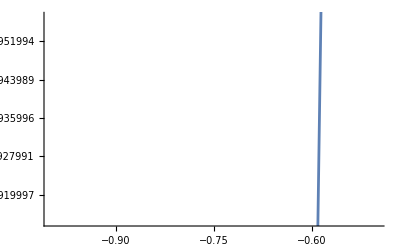

```mathematica
Plot[α,{y,-1,-0.5}]
```

```mathematica
α1=(1-0.1 A y(Ni-1)^2/(Ni^2-1))/(1-0.1A y(Ni-1)^2/Ni^2)/.{Ni->1.5187228,A->0.25};
Plot[α1,{y,-1,-0.5}]
```

-Graphics-

In other words, α is very next to 1. Instead of the above expression of α, we use the following other

```mathematica
α=Δ(Ni^2-1)/(α Ni^2)
```

(0.566446 ((2.77556×10^-17+0.172002 r3)^2+0.600913 (0.150228+0.172002 r3-0.00472009 r3^2)) (1+1.11968×10^-12 y))/(1+1.97667×10^-12 y)

where α varies from 0.95 to 1. It is possible to verify that for α=0.975 the rays of different colors intercepting the corrector at 0.7 D arrive at the same point on the axis. Finally, if α=0.95 that happens to the maarginal rays.

# The program

```mathematica
MCamera[f_,ind_,diam_,α_,waves_,sf_,co_,cr_]:=
Module[{},

(* Spherical aberration of the mirror *)
DS1=-1/(32 f^3);

(*Meniscus*)
sost0={Ni->ind[[1,2]],Δ->0.1diam};
(* Difference of radii and spherical aberration and coma *)
s= Δ(Ni^2-1)/Ni^2//.sost0;
DC1=(Ni-1)/(8 Ni^2 r1^4)(-r1+1/(Ni (r1-s)^3)(r1+(-1+Ni) (s-Δ))^2 (Ni (r1-Δ)+Δ) (r1+(-1+Ni) (s+Ni s-Ni Δ)))//.sost0;

eq0=Together[DS1+DC1]//Numerator;
sol=NSolve[eq0==0,r1,10];
m1=Table[If[Head[sol[[i,1,2]]]===Complex||Sign[sol[[i,1,2]]]==1,0,sol[[i]]],{i,1,Length[sol]}]//Flatten;
m2=DeleteCases[m1,0];
m3=DeleteCases[Table[If[m2[[i,2]]>-80,0,m2[[i]]],{i,Length[m2]}],0];
r11=m3[[1,2]];

TotalAberrations[{R1,R1-s,-2f},{0.1diam,β f},ind,{0,0,0},diam/2,0,0,-Infinity,x,α,waves,2];
sol1=FindRoot[{Absftot[1]==0,Comatot[1]==0},{R1,r11},{β,1},MaxIterations->50];

HOrdAberrations[{sol1[[1,2]],sol1[[1,2]]-s,-2f},{0.1diam,sol1[[2,2]] f},ind,{0,0,0},diam/2,0,0,-Infinity,y,α,waves,2];
sf5=sfer5;
co5=coma5;

MarginalRayTracing[{sol1[[1,2]],sol1[[1,2]]-s,-2f},{0.1 diam, sol1[[2,2]] f},ind,{0,0,0},diam/2,0,0,-Infinity,y,α,waves,2];
margcr=(znu[2]-znu[3]);

TotalAberrations[{R2,R3,-2fot},{0.1diam,δ f},ind,{0,0,0},diam/2,0,0,-Infinity,y,α,waves,2];
sol2=FindRoot[{Absftot[1]==- sf sf5,Comatot[1]==-co co5,2(zog1[2,n]-zog1[3,n])==-cr margcr,foc[1]==-f},{R2,sol1[[1,2]]},{R3,sol1[[1,2]]-s},{δ,sol1[[2,2]]},{fot,f},MaxIterations->100];
ff=foc[1]/.sol2;
TotalAberrations[{sol2[[1,2]],sol2[[2,2]],-2sol2[[4,2]]},{0.1diam,sol2[[3,2]] f},ind,{0,0,0},diam/2,0,0,-Infinity,x,α,waves,2];
HOrdAberrations[{sol2[[1,2]],sol2[[2,2]],-2sol2[[4,2]]},{0.1diam,sol2[[3,2]] f},ind,{0,0,0},diam/2,0,0,-Infinity,y,α,waves,2];
sf6=sfer5;
co6=coma5;

MarginalRayTracing[{sol2[[1,2]],sol2[[2,2]],-2sol2[[4,2]]},{0.1diam,sol2[[3,2]] f},ind,{0,0,0},diam/2,0,0,-Infinity,y,α,waves,2];
margcrf=(znu[2]-znu[3]);

Print["Focal lenght = ",ff];
Print["Anterior curvature radius of corrector = ",sol2[[1,2]]];
Print["Posterior curvature radius of corrector = ",sol2[[2,2]]];
Print["Primary radius = ",-2sol2[[4,2]]];
Print["Thickness of corrector = ", 0.1 diam];
Print["Distance of the primary mirror from corrector = ",sol2[[3,2]] f];
Print["Third-order spherical aberration = ",Absftot[1]];
Print["Fifth-order spherical aberration = ",sf6];
Print["Third-order coma = ",Comatot[1]];
Print["Fifth-order coma = ",co6];
Print["Axial chromatism = ", zog1[2,n]-zog1[3,n]];
Print["Marginal chromatism = ",margcrf];

]
```

```mathematica
f=600;
ind=ind={{1,1.5187228,1,-1},{1,1.522376,1,-1},{1,1.514322,1,-1}}; (*BK7*)
diam=200;
α=1.5;
waves={λ1,λ2,λ3};
sf=0.72;
co=0.73;
cr=1;
MCamera[f,ind,diam,α,waves,sf,co,cr]
```

Focal lenght = -600.

Anterior curvature radius of corrector = -248.783

Posterior curvature radius of corrector = -260.59

Primary radius = -1240.6

Thickness of corrector = 20.

Distance of the primary mirror from corrector = 780.469

Third-order spherical aberration = -0.034603

Fifth-order spherical aberration = 0.0343487

Third-order coma = 0.00635903

Fifth-order coma = -0.00626282

Axial chromatism = -0.0181401

Marginal chromatism = 0.0017443

```mathematica
ind={{1,1.5187228,1,-1},{1,1.522376,1,-1},{1,1.514322,1,-1}}; (*BK7*)
waves={λ1,λ2,λ3};
sf=0.75;
co=0.76;
cr=1;
MCamera[700,ind,200,1.3,waves,sf,co,cr]
```

Focal lenght = -700.

Anterior curvature radius of corrector = -276.511

Posterior curvature radius of corrector = -288.205

Primary radius = -1443.93

Thickness of corrector = 20.

Distance of the primary mirror from corrector = 932.732

Third-order spherical aberration = -0.0208637

Fifth-order spherical aberration = 0.0209799

Third-order coma = 0.00374092

Fifth-order coma = -0.00374718

Axial chromatism = -0.0148049

Marginal chromatism = 0.00282344

```mathematica
ind={{1,1.5187228,1,-1},{1,1.522376,1,-1},{1,1.514322,1,-1}}; (*BK7*)
waves={λ1,λ2,λ3};
sf=0.75;
co=0.8;
cr=1;
MCamera[800,ind,200,1.3,waves,sf,co,cr]
```

Focal lenght = -800.

Anterior curvature radius of corrector = -303.513

Posterior curvature radius of corrector = -315.136

Primary radius = -1646.87

Thickness of corrector = 20.

Distance of the primary mirror from corrector = 1084.53

Third-order spherical aberration = -0.0130014

Fifth-order spherical aberration = 0.0136368

Third-order coma = 0.0027209

Fifth-order coma = -0.00270144

Axial chromatism = -0.0125753

Marginal chromatism = 0.00316392

# Maksutov Achromatic Camera

In front of the main mirror S there is a Maksutov meniscus whose surfaces have their centers at the center of S. Moreover, at this point there is a convergent lens to make achromatic the combination. spess is the thickness of the lens and sfe is the arbitrary value of the third-order spherical aberration starting from zero. It is convenient to increase the distance between the meniscus and the mirror of a few millimetres  to reduce the third-order coma.

```mathematica
Off[RowReduce::luc];

MAchromaticCamera[f_,ind_,diam_,α_,waves_,spess_,sf_,cr_]:=
Module[{},


(* First, we suppose that there is no convergent lens. The spherical aberration of the meniscus balances the corresponding aberration of the mirror with its aperture stop at a distance -2f*)
TotalAberrations[{Infinity ,Infinity,-Δ1,-Δ1-0.1diam,-2f },{0,Δ1,0.1diam,2f-(Δ1+0.1 diam)},ind,{0,0,0,0,0},diam/2,0,0,-Infinity,y,α,waves,2];

esf=Numerator[Together[Absftot[1]]];
s0=NSolve[esf==0,Δ1];
s00=Table[s0[[i]][[1,2]],{i,1,Length[s0]}];
s000=Cases[s00,_Real];
su=Select[s000,Sign[#]>0&];
corr=Max[su];


(* The approximate value of the radius of the first lens to achromatize the system *)
TotalAberrations[{1/cu1 ,-1/cu1,-Δ2 f,-Δ2 f-0.1diam,1/cu2},{spess,Δ2 f-spess/2,0.1diam,-1/cu2-(Δ2 f+0.1 diam)},ind,{0,0,0,0,0},diam/2,0,0,-Infinity,y,α,waves,2];
abc=Absftot[1];
fff1=foc[1];
zzz1=zog1[2,n]-zog1[3,n];
sol1=FindRoot[{abc==0,fff1==-f,zzz1==0},{cu1,10^-5},{Δ2,corr/f},{cu2,-1/(2f)}];

HOrdAberrations[{1/sol1[[1,2]] ,-1/sol1[[1,2]],-sol1[[2,2]]f,-sol1[[2,2]]f-0.1diam,1/sol1[[3,2]]},{spess,sol1[[2,2]]f-spess/2,0.1diam,-1/sol1[[3,2]]-(sol1[[2,2]]f+0.1 diam)},ind,{0,0,0,0,0},diam/2,0,0,-Infinity,y,α,waves,2];

sf5=sfer5;
co5=coma5;

MarginalRayTracing[{1/sol1[[1,2]] ,-1/sol1[[1,2]],-sol1[[2,2]]f,-sol1[[2,2]]f-0.1diam,1/sol1[[3,2]]},{spess,sol1[[2,2]]f-spess/2,0.1diam,-1/sol1[[3,2]]-(sol1[[2,2]]f+0.1 diam)},ind,{0,0,0,0,0},diam/2,0,0,-Infinity,y,α,waves,2];
margcr=(znu[2]-znu[3]);

(*Final calculations *)
TotalAberrations[{1/bu1,-1/bu1,-Δ3 f,-Δ3 f-0.1diam,1/bu2},{spess,Δ3 f-spess/2,0.1diam,-1/bu2-(Δ3 f+0.1 diam)},ind,{0,0,0,0,0},diam/2,0,0,-Infinity,y,α,waves,2];
abc2=Absftot[1];
fff2=foc[1];
zzz2=zog1[2,n]-zog1[3,n];
sol2=FindRoot[{abc2==-sf sf5,fff2==-f,zzz2==-cr margcr},{bu1,sol1[[1,2]]},{Δ3,sol1[[2,2]]},{bu2,sol1[[3,2]]}];
TotalAberrations[{1/sol2[[1,2]],-1/sol2[[1,2]],-sol2[[2,2]]f,-sol2[[2,2]]f-0.1 diam,1/sol2[[3,2]]},{spess,sol2[[2,2]]f-spess/2,0.1diam, -1/sol2[[3,2]]-(sol2[[2,2]]f+0.1 diam)},ind,{0,0,0,0,0},diam/2,0,0,-Infinity,x,α,waves,2];
HOrdAberrations[{1/sol2[[1,2]],-1/sol2[[1,2]],-sol2[[2,2]]f,-sol2[[2,2]]f-0.1 diam,1/sol2[[3,2]]},{spess,sol2[[2,2]]f-spess/2,0.1diam, -1/sol2[[3,2]]-(sol2[[2,2]]f+0.1 diam)},ind,{0,0,0,0,0},diam/2,0,0,-Infinity,x,α,waves,2];
abc3=Absftot[1];
fff3=foc[1];
zzz3=zog1[2,n]-zog1[3,n];
sf6=sfer5;
co6=coma5;

MarginalRayTracing[{1/sol2[[1,2]],-1/sol2[[1,2]],-sol2[[2,2]]f,-sol2[[2,2]]f-0.1 diam,1/sol2[[3,2]]},{spess,sol2[[2,2]]f-spess/2,0.1diam, -1/sol2[[3,2]]-(sol2[[2,2]]f+0.1 diam)},ind,{0,0,0,0,0},diam/2,0,0,-Infinity,x,α,waves,2];
margcrf=(znu[2]-znu[3]);
Print["First radius of the lens = ",1/sol2[[1,2]]];
Print["Second radius of the lens = ",-1/sol2[[1,2]]];
Print["First radius of corrector = ",-sol2[[2,2]]f];
Print["Second radius of corrector = ",-sol2[[2,2]]f-0.1diam];
Print["Thickness of corrector = ", 0.1 diam];
Print["Radius of mirror = ",1/sol2[[3,2]]];
Print["Focal length = ",fff2/.sol2];
Print["Distance between the lens and the corrector = ",sol2[[2,2]]f-spess/2];
Print["Distance of the primary mirror from corrector = ",-(1/sol2[[3,2]])-(spess +sol2[[2,2]]f+0.1 diam)];
Print["Third-order spherical aberration = ",Absftot[1]];
Print["Fifth-order spherical aberration = ",sf6];
Print["Third-order coma = ",Comatot[1]];
Print["Fifth-order coma = ",co6];
Print["Axial chromatism = ", zog1[2,n]-zog1[3,n]];
Print["Marginal chromatism = ",margcrf]

]
```

```mathematica
f=600;
ind={{1,1.5187228,1,1.5187228,1,-1},{1,1.522376,1,1.522376,1,-1},{1,1.514322,1,1.514322,1,-1}}; (*BK7*)
diam =200;
α =2;
waves={λ1,λ2,λ3};
sf=0.9;
cr=1;
spess=10;
MAchromaticCamera[f,ind,diam,α,waves,spess,sf,cr]
```

First radius of the lens = 24746.6

Second radius of the lens = -24746.6

First radius of corrector = -328.005

Second radius of corrector = -348.005

Thickness of corrector = 20.

Radius of mirror = -1213.14

Distance between the lens and the corrector = 323.005

Distance of the primary mirror from corrector = 855.131

Third-order spherical aberration = -0.0215103

Fifth-order spherical aberration = 0.0211744

Third-order coma = 0.00023257

Fifth-order coma = -0.0000381449

Axial chromatism = 0.0138986

Marginal chromatism = 0.000698133

Focal length = -600.

```mathematica
f=500;
ind={{1,1.5187228,1,1.5187228,1,-1},{1,1.522376,1,1.522376,1,-1},{1,1.514322,1,1.514322,1,-1}}; (*BK7*)
diam =200;
α =2.2;
waves={λ1,λ2,λ3};
spess=5;
sf=0.87;
cr=0.9;
MAchromaticCamera[f,ind,diam,α,waves,spess,sf,cr]
```

First radius of the lens = 18748.7

Second radius of the lens = -18748.7

First radius of corrector = -286.013

Second radius of corrector = -306.013

Thickness of corrector = 20.

Radius of mirror = -1011.54

Focal length = -500.

Distance between the lens and the corrector = 283.513

Distance of the primary mirror from corrector = 700.525

Third-order spherical aberration = -0.0386162

Fifth-order spherical aberration = 0.037962

Third-order coma = 0.000378758

Fifth-order coma = -0.00012433

Axial chromatism = 0.0151674

Marginal chromatism = -0.00063638

```mathematica
f=500;
ind={{1,1.5187228,1,1.5187228,1,-1},{1,1.522376,1,1.522376,1,-1},{1,1.514322,1,1.514322,1,-1}}; (*BK7*)
diam =200;
α =2.2;
waves={λ1,λ2,λ3};
spess=5;
sf=0.87;
cr=1;
MAchromaticCamera[f,ind,diam,α,waves,spess,sf,cr]
```

```mathematica
f=480;
ind={{1,1.5187228,1,1.5187228,1,-1},{1,1.522376,1,1.522376,1,-1},{1,1.514322,1,1.514322,1,-1}}; (*BK7*)
diam =200;
α =2.5;
waves={λ1,λ2,λ3};
spess=5;
sf=0.85;
cr=0.9;
MAchromaticCamera[f,ind,diam,α,waves,spess,sf,cr]
```

First radius of the lens = 17575.9

Second radius of the lens = -17575.9

First radius of corrector = -277.299

Second radius of corrector = -297.299

Thickness of corrector = 20.

Radius of mirror = -971.162

Distance between the lens and the corrector = 274.799

Distance of the primary mirror from corrector = 668.862

Third-order spherical aberration = -0.0433262

Fifth-order spherical aberration = 0.0433023

Third-order coma = 0.000469762

Fifth-order coma = -0.000165886

Axial chromatism = 0.0158412

Marginal chromatism = -0.000641016

Focal length = -480.